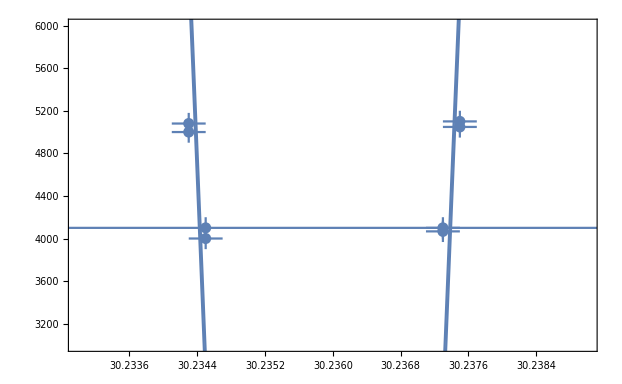

```mathematica
Needs["EDA`"]
mydata={{{30.2343,0.0002},{5000,100}},{{30.2373,.0002},{4067,100}},{{30.2375,.0002},{5048,100}},{{30.2345,.0002},{4000,100}}};
mydata2={{{30.2343,0.0002},{5080,100}},{{30.2373,.0002},{4100,100}},{{30.2375,.0002},{5100,100}},{{30.2345,.0502},{4100,100}}};
Show[{EDAListPlot[mydata,PlotRange->{{30.233,30.239},{3000,6000}}],EDAListPlot[mydata2,PlotRange->{{30.233,30.239},{3000,6000}}],Plot[b1+a1 Cos[ 2π(xx-p1)2/ww ],{xx,30.233,30.239}],Plot[b1+a1 Cos[ 2π(xx-p1-.00002)2/ww ],{xx,30.233,30.239}]},Frame->True,PlotLegends->{"Data:+HV","Fit: +HV","Fit:-HV"}]
mydata2={{30.08351718,5128},{30.12281397,4467},{30.27830386,4448},{30.34715207,5154},{30.35860257,5000}};
```

FittedModel::constr: The property values {"ParameterTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
aa | 6395.64 | 5446.43 | 1.17428 | 0.361174
p | 30.0348 | 0.000154426 | 194494. | 2.64356×10^-11
bb | 19.779 | 3575.65 | 0.00553157 | 0.996089

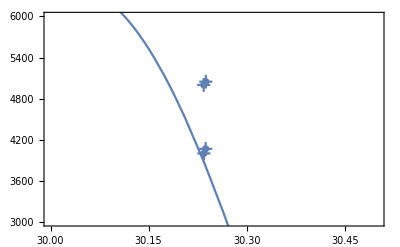

```mathematica
Teff=180+8/Pi;
ww=1/Teff;
nlm100=NonlinearModelFit[mydata2,{aa Cos[ 2π(xx-p)2/ww]+bb,{p>30,p<31}},{aa,p,bb},{xx},Method->{"NMinimize"}];
nlm100["ParameterTable"]
a1=aa/.nlm100[[1]][[2]];
b1=bb/.nlm100[[1]][[2]];
p1=p/.nlm100[[1]][[2]];
Show[{EDAListPlot[mydata,PlotRange->{{30.0,30.5},{3000,6000}}],Plot[b1+a1 Cos[ (xx-p1)Teff/(2π)^2 ],{xx,29.5,31}]},Frame->True]
```

FittedModel::constr: The property values {"ParameterTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
aa | 17185.3 | 12809.2 | 1.34163 | 0.407771
p | 30.4742 | 0.0000748644 | 407058. | 1.56395×10^-6
bb | 1975.52 | 2387.75 | 0.827358 | 0.559967

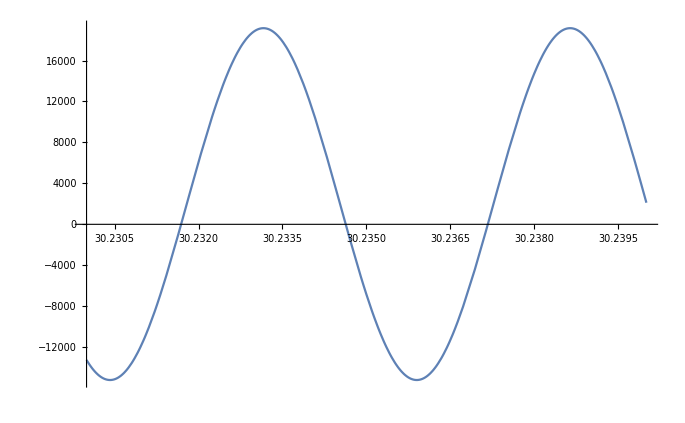

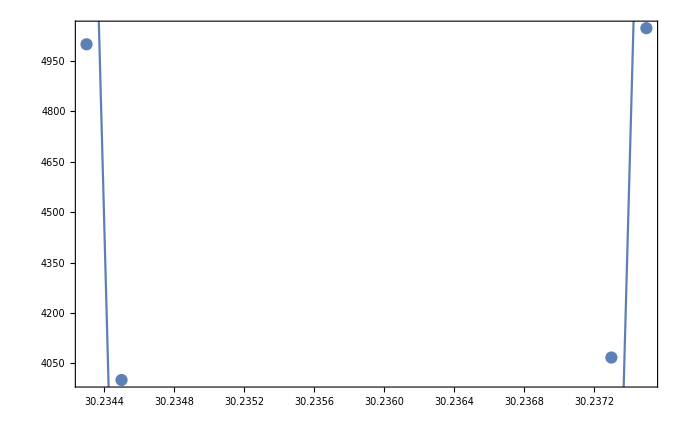

```mathematica
ww=2/Teff;
mydata2={{30.2343,5000},{30.2373,4067},{30.2375,5048},{30.2345,4000}};
nlm100=NonlinearModelFit[mydata2,{aa Cos[ 2π(xx-p)2/ww]+bb,{p>30,p<31}},{aa,p,bb},{xx},Method->{"NMinimize"}];
nlm100["ParameterTable"]
a1=aa/.nlm100[[1]][[2]];
b1=bb/.nlm100[[1]][[2]];
p1=p/.nlm100[[1]][[2]];
Plot[b1+a1 Cos[ 2π(xx-p1)2/ww],{xx,30.23,30.24}]
Show[{ListPlot[mydata2],Plot[b1+a1 Cos[ 2π(xx-p1)2/ww ],{xx,30.23,30.24}]},Frame->True]
```

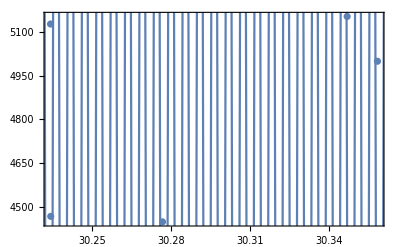

```mathematica
Show[{EDAListPlot[mydata2],Plot[b1+a1 Cos[ 2π(xx-p1)1/ww ],{xx,29.5,31}]},Frame->True]
```

```mathematica
N[ww]
ww
```

0.00547806

1/(180+8/π)